## D_4 molecular orbitals

### Set 1

```mathematica
D4=<|
"Irreps"->{"A_1","A_2","B_1","B_2","E"},
"CharacterTable"->
{
{1,1,1,1,1},
{1,1,1,-1,-1},
{1,-1,1,1,-1},
{1,-1,1,-1,1},
{2,0,-2,0,0}
},
"ConjugacyClasses"->{"E","C_4","C_2^z","C'_2","C''_2"},
"ConjugacyClassSizes"->{1,2,1,2,2}
|>;
```

```mathematica
OrbBasis={p1,p2,p3,p4};
D4gens={
(*Subscript[C, 4]^+*)({{0, 0, 0, 1}, {1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 1, 0}}),
(*Subscript[C, 2]'(x)*)({{1, 0, 0, 0}, {0, 0, 0, 1}, {0, 0, 1, 0}, {0, 1, 0, 0}})
};
MatrixForm/@(D4mats=Flatten[Table[MatrixPower[D4gens[[1]],i].MatrixPower[D4gens[[2]],j],{i,0,3},{j,0,1}],1])
```

{(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 0),(0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0),(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0),(0 | 0 | 1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | 1 | 0 | 0),(0 | 0 | 1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1),(0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0),(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0)}

```mathematica
D4matClasses={"E","C'_2","C_4","C''_2","C_2^z","C'_2","C_4","C''_2"};
```

```mathematica
projectorD4[irrep_]:=Module[{repind},
repind=Position[D4["Irreps"],irrep][[1,1]];
(D4["CharacterTable"][[repind,1]])/8∑_(i=1)^8 D4["CharacterTable"][[repind,Position[D4["ConjugacyClasses"],D4matClasses[[i]]][[1,1]]]]D4mats[[i]]
]
```

```mathematica
projectors={PA1,PA2,PB1,PB2,PE}=projectorD4/@D4["Irreps"];
```

```mathematica
TableForm[{MatrixForm/@projectors},TableHeadings->{None,D4["Irreps"]}]
```

A_1 | A_2 | B_1 | B_2 | E
(1/4 | 1/4 | 1/4 | 1/4
1/4 | 1/4 | 1/4 | 1/4
1/4 | 1/4 | 1/4 | 1/4
1/4 | 1/4 | 1/4 | 1/4) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (1/4 | -1/4 | 1/4 | -1/4
-1/4 | 1/4 | -1/4 | 1/4
1/4 | -1/4 | 1/4 | -1/4
-1/4 | 1/4 | -1/4 | 1/4) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (1/2 | 0 | -1/2 | 0
0 | 1/2 | 0 | -1/2
-1/2 | 0 | 1/2 | 0
0 | -1/2 | 0 | 1/2)

```mathematica
#.#==#&/@projectors
```

{True,True,True,True,True}

```mathematica
PA1.OrbBasis
```

{p1/4+p2/4+p3/4+p4/4,p1/4+p2/4+p3/4+p4/4,p1/4+p2/4+p3/4+p4/4,p1/4+p2/4+p3/4+p4/4}

```mathematica
(*Or ψ'=Pψ, then Pψ'=ψ', ψ' is an eigen vector of P.*)
```

```mathematica
Eigensystem[PA1]
```

{{1,0,0,0},{{1,1,1,1},{-1,0,0,1},{-1,0,1,0},{-1,1,0,0}}}

```mathematica
Normalize[{1,1,1,1}].OrbBasis
```

p1/2+p2/2+p3/2+p4/2

```mathematica
Eigensystem[PB1]
```

{{1,0,0,0},{{-1,1,-1,1},{1,0,0,1},{-1,0,1,0},{1,1,0,0}}}

```mathematica
Normalize[-{-1,1,-1,1}].OrbBasis
```

p1/2-p2/2+p3/2-p4/2

```mathematica
Eigensystem[PE]
```

{{1,1,0,0},{{0,-1,0,1},{-1,0,1,0},{0,1,0,1},{1,0,1,0}}}

```mathematica
Normalize[{0,-1,0,1}].OrbBasis
Normalize[{-1,0,1,0}].OrbBasis
```

-p2/(√2)+p4/(√2)

-p1/(√2)+p3/(√2)

### Set 2

```mathematica
D4=<|
"Irreps"->{"A_1","A_2","B_1","B_2","E"},
"CharacterTable"->
{
{1,1,1,1,1},
{1,1,1,-1,-1},
{1,-1,1,1,-1},
{1,-1,1,-1,1},
{2,0,-2,0,0}
},
"ConjugacyClasses"->{"E","C_4","C_2^z","C'_2","C''_2"},
"ConjugacyClassSizes"->{1,2,1,2,2}
|>;
```

```mathematica
OrbBasis={p1,p2,p3,p4};
D4gens={
(*Subscript[C, 4]^+*)({{0, 0, 0, 1}, {1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 1, 0}}),
(*Subscript[C, 2]'(x)*)({{-1, 0, 0, 0}, {0, 0, 0, -1}, {0, 0, -1, 0}, {0, -1, 0, 0}})
};
MatrixForm/@(D4mats=Flatten[Table[MatrixPower[D4gens[[1]],i].MatrixPower[D4gens[[2]],j],{i,0,3},{j,0,1}],1])
```

{(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(-1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | -1 | 0
0 | -1 | 0 | 0),(0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0),(0 | -1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | -1 | 0),(0 | 0 | 1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | 1 | 0 | 0),(0 | 0 | -1 | 0
0 | -1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | -1),(0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0),(0 | 0 | 0 | -1
0 | 0 | -1 | 0
0 | -1 | 0 | 0
-1 | 0 | 0 | 0)}

```mathematica
D4matClasses={"E","C'_2","C_4","C''_2","C_2^z","C'_2","C_4","C''_2"};
```

```mathematica
projectorD4[irrep_]:=Module[{repind},
repind=Position[D4["Irreps"],irrep][[1,1]];
(D4["CharacterTable"][[repind,1]])/8∑_(i=1)^8 D4["CharacterTable"][[repind,Position[D4["ConjugacyClasses"],D4matClasses[[i]]][[1,1]]]]D4mats[[i]]
]
```

```mathematica
projectors={PA1,PA2,PB1,PB2,PE}=projectorD4/@D4["Irreps"];
```

```mathematica
TableForm[{MatrixForm/@projectors},TableHeadings->{None,D4["Irreps"]}]
```

A_1 | A_2 | B_1 | B_2 | E
(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (1/4 | 1/4 | 1/4 | 1/4
1/4 | 1/4 | 1/4 | 1/4
1/4 | 1/4 | 1/4 | 1/4
1/4 | 1/4 | 1/4 | 1/4) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (1/4 | -1/4 | 1/4 | -1/4
-1/4 | 1/4 | -1/4 | 1/4
1/4 | -1/4 | 1/4 | -1/4
-1/4 | 1/4 | -1/4 | 1/4) | (1/2 | 0 | -1/2 | 0
0 | 1/2 | 0 | -1/2
-1/2 | 0 | 1/2 | 0
0 | -1/2 | 0 | 1/2)

```mathematica
#.#==#&/@projectors
```

{True,True,True,True,True}

```mathematica
(*Or ψ'=Pψ, then Pψ'=ψ', ψ' is an eigen vector of P.*)
```

```mathematica
Eigensystem[PA2]
```

{{1,0,0,0},{{1,1,1,1},{-1,0,0,1},{-1,0,1,0},{-1,1,0,0}}}

```mathematica
Normalize[{1,1,1,1}].OrbBasis
```

p1/2+p2/2+p3/2+p4/2

```mathematica
Eigensystem[PB2]
```

{{1,0,0,0},{{-1,1,-1,1},{1,0,0,1},{-1,0,1,0},{1,1,0,0}}}

```mathematica
Normalize[-{-1,1,-1,1}].OrbBasis
```

p1/2-p2/2+p3/2-p4/2

```mathematica
Eigensystem[PE]
```

{{1,1,0,0},{{0,-1,0,1},{-1,0,1,0},{0,1,0,1},{1,0,1,0}}}

```mathematica
Normalize[{0,-1,0,1}].OrbBasis
Normalize[{-1,0,1,0}].OrbBasis
```

-p2/(√2)+p4/(√2)

-p1/(√2)+p3/(√2)

### Set 3

Set 3 identical to set 2 in terms of representation matrices, where the basis set consists of pz orbitals pointing up.

## Emery three-orbital TB model

```mathematica
Needs["MathTB`TightBinding`"]
```

Loaded the MathTB Package: TightBinding library - version 0.1.0

Written by Yi Lu

```mathematica
PlotBand[Energy_,Knames_,Emin_,Emax_,ratio_:0.7]:=ListPlot[
Energy,Joined->True,
PlotRange->{{0.9,Length[Energy[[1]]]+0.1},{Emin,Emax}},
Frame->True,FrameStyle->Thickness[0.0015],FrameTicks->{Reverse[#]&/@Knames,Automatic},FrameTicksStyle->Directive[FontFamily->"Times New Roman",FontSize->12,Black,Italic],
AspectRatio->ratio,PlotStyle->{RGBColor[1,0,0]},
GridLines->{Knames[[;;,2]],{}},GridLinesStyle->{{Black,Thickness[0.0015]},{}}
]
```

```mathematica
lat={{1,0},{0,1}};
orb={{0,0},{0.5,0},{0,0.5}};
emeryTB=InitTightBindingModel[2,2,lat,orb]
```

Periodic (infinite) in all dimensons.

Hamiltonian constructed with 1 spin(s).

<|dimk→2,dimr→2,lat→{{1,0},{0,1}},orb→{{0,0},{0.5,0},{0,0.5}},norb→3,per→{1,2},nspin→1,onsite→{0,0,0},hoppings→{}|>

```mathematica
tpd=1.0;
SetOnSite[emeryTB,{-1.0,-4.0,-4.0}]
SetHoppings[emeryTB,tpd,1,2,{0,0}];
SetHoppings[emeryTB,-tpd,1,3,{0,0}];
SetHoppings[emeryTB,-tpd,1,2,{-1,0}];
SetHoppings[emeryTB,tpd,1,3,{0,-1}];
```

<|dimk→2,dimr→2,lat→{{1,0},{0,1}},orb→{{0,0},{0.5,0},{0,0.5}},norb→3,per→{1,2},nspin→1,onsite→{-1.,-4.,-4.},hoppings→{}|>

```mathematica
Chop[FullSimplify[ExpToTrig[CreateHamiltonian[emeryTB,{kx,ky}]],{kx,ky,mu,tpd}∈Reals]]//MatrixForm
```

(-1. | (0.+2. ⅈ) Sin[3.14159 kx] | (0.-2. ⅈ) Sin[3.14159 ky]
(0.-2. ⅈ) Sin[3.14159 kx] | -4. | 0
(0.+2. ⅈ) Sin[3.14159 ky] | 0 | -4.)

```mathematica
HTBemery[{kx_,ky_}]:=({{-1.0, 2 ⅈ Sin[π kx], -2 ⅈ Sin[π ky]}, {-2 ⅈ Sin[π kx], -4, 0}, {2 ⅈ Sin[π ky], 0, -4}})
```

```mathematica
KPathDefine={
{"G",{0.0, 0.0},40},
{"X",{0.5,0},40},
{"M",{0.5,0.5},57},
{"G",{0.0, 0.0},1},
{"G",{0.0, 0.0},0}
};
KPoints=Flatten[Table[Table[KPathDefine[[i,2]](KPathDefine[[i,3]]-j+1)/KPathDefine[[i,3]]+KPathDefine[[i+1,2]](j-1)/KPathDefine[[i,3]],{j,1,KPathDefine[[i,3]]}],{i,1,Length[KPathDefine]-1}],1];
Knames=Table[{KPathDefine[[i,1]],1+Sum[KPathDefine[[ii,3]],{ii,1,i-1}]},{i,1,Length[KPathDefine]-1}];
```

```mathematica
TBval=Chop[Sort[Eigenvalues[HTBemery[#]]]&/@KPoints];
```

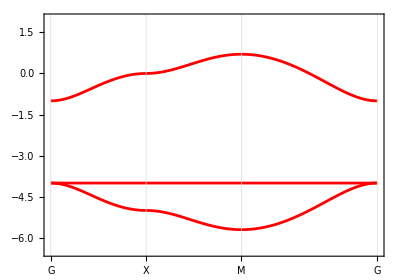

```mathematica
PlotBand[Transpose[TBval],Knames,-6.5,2]
```